```mathematica
SetDirectory["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Практика\\Программа\\project"];
```

```mathematica
(*Определение положения точки*)
```

```mathematica
determinePointPosition[lineStartPoint_,lineEndPoint_,pointToCheck_]:=
Block[{result,positionLine},
result:=(pointToCheck[[1]]-lineStartPoint[[1]])*(lineEndPoint[[2]]-lineStartPoint[[2]])-(pointToCheck[[2]]-lineStartPoint[[2]])*(lineEndPoint[[1]]-lineStartPoint[[1]]);
positionLine:=Which[result<0,"down",result>0,"up",result==0,"within" ]; positionLine]
```

```mathematica
(*Визуализация*)
vizualization[File_String]:=Block[{Points =Rest@Import[File, "Table"], ConvexHull = SimpleSearchConvexHullFile[File]},Graphics[{Point@Points, Red,Line@Append[ConvexHull,ConvexHull[[1]]]}]];


(*Метод перебора*)
```

```mathematica
SimpleSearchConvexHull[Points_List] := Block[{points=Points,n,convexHullPoints = {},pointWithXmin,formerPoint,latterPoint,areOnTheSameSide,comparator,currentPointPosition,indexMinXCoord,i,indexInPoints},
n =Length[points];(*количество точек*)
(*Нахождение нижней точки из самых левых*)
For[i= 2;indexMinXCoord=1, i≤ n, i+=1,
If[points⟦i,1⟧<points⟦indexMinXCoord,1⟧ || 
points⟦i,1⟧==points⟦indexMinXCoord,1⟧ &&  
points⟦i,2⟧<points⟦indexMinXCoord,2⟧,
indexMinXCoord=i;indexMinXCoord]];
pointWithXmin=points[[indexMinXCoord]];
points=Delete[points,indexMinXCoord];
PrependTo[points,pointWithXmin];
AppendTo[convexHullPoints,pointWithXmin];
formerPoint=convexHullPoints[[Length[convexHullPoints]]];
For[i=2,i≤ n ,++i, 
latterPoint=points[[i]];
areOnTheSameSide=True;
indexInPoints=1;
comparator="within";

For[indexInPoints=1,indexInPoints≤ n , ++indexInPoints,

If[comparator!= "within",++indexInPoints;Break[];];
comparator=determinePointPosition[formerPoint,latterPoint,points[[indexInPoints]]]];
For[Null,indexInPoints≤ n , ++indexInPoints, 
currentPointPosition=determinePointPosition[formerPoint,latterPoint,points[[indexInPoints]]];
If[((currentPointPosition≠comparator)&&(currentPointPosition≠"within")),
areOnTheSameSide=False;Break[], 
Null]
];
If[(areOnTheSameSide)&& !(MemberQ[convexHullPoints,latterPoint]),
 AppendTo[convexHullPoints,latterPoint];
formerPoint=latterPoint;i=0]];convexHullPoints];
SimpleSearchConvexHullFile[from_String]:=Block[{list=Rest@Import[from, "Table"], result,time},result=SimpleSearchConvexHull[list];Print[Length@result ];result];
```

```mathematica
Timing@SimpleSearchConvexHullFile["question.txt"]
```

24

{5.90625,{{-0.999878,-0.0851772},{-0.999512,0.947508},{-0.998535,0.979797},{-0.763909,0.993408},{-0.355022,0.997253},{0.20658,0.999573},{0.784906,0.999207},{0.878475,0.995849},{0.947569,0.978027},{0.993225,0.841365},{0.999695,0.506882},{0.999878,0.19071},{0.999084,-0.268654},{0.986633,-0.882076},{0.982299,-0.975646},{0.821223,-0.995849},{0.229041,-0.998474},{-0.370647,-1},{-0.649098,-0.998169},{-0.909421,-0.988769},{-0.961974,-0.983581},{-0.97644,-0.925352},{-0.988525,-0.851375},{-0.996277,-0.588916}}}

24

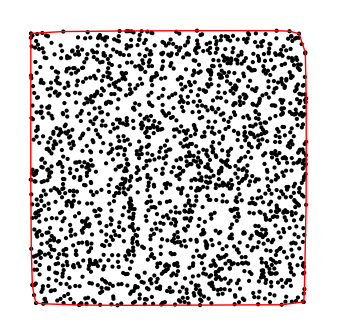

```mathematica
vizualization["question.txt"]
```